```mathematica
ClearAll["Global`*"]
```

```mathematica
a=0.2;
b=0.1;
L=1.25415659428362;
```

```mathematica
f[t_]:={0.5+a Cos[2π t](1-Sin[2π t ]),0.5+ b Sin[2 π t](1+Cos[2 π t])}
```

```mathematica
λ[t_]:=NIntegrate[Norm[f'[s]],{s,0,t}]
```

```mathematica
(*1 test scalar*)
```

```mathematica
(*1.1 2d -> 1d *)
```

```mathematica
u01[x_]:=1+3 x[[1]]^2+2*x[[2]]^2
```

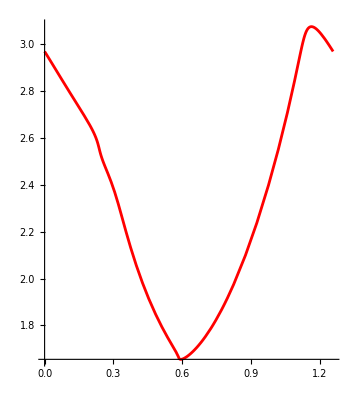

```mathematica
plotex=ParametricPlot[{λ[t],u01[f[t]]},{t,0,1},PlotStyle->Red]
```

```mathematica
t=Import["/Users/michelecastellana/Documents/finite_elements/poisson_equation/solve_u/three_domains/solution/u_1d.csv"];
t= Table[{t[[i,2]],t[[i,1]]},{i,2,Length[t]}]
```

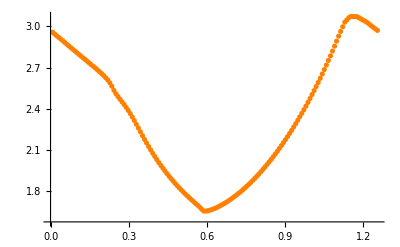

```mathematica
plotnum=ListPlot[t,PlotStyle->Orange]
```

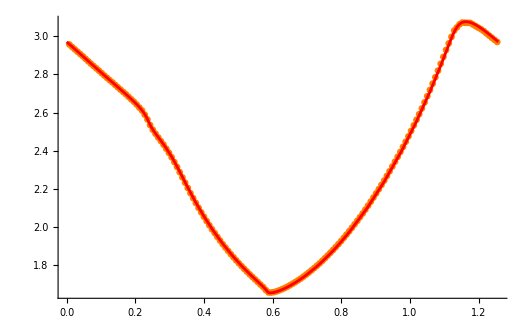

```mathematica
Show[plotnum,plotex,PlotRange->Full]
```

```mathematica
(*1.1 1d -> 2d *)
```

```mathematica
u1[x_]:=Cos[2π x/L]
```

```mathematica
plotex=ParametricPlot3D[Flatten[{f[t],u1[λ[t]]}],{t,0,1},PlotStyle->Blue]
```

-Graphics3D-

```mathematica
t=Import["/Users/michelecastellana/Documents/finite_elements/poisson_equation/solve_u/three_domains/solution/u_2d.csv"];
t= Table[{t[[i,2]],t[[i,3]],t[[i,1]]},{i,2,Length[t]}]
```

```mathematica
plotnum=ListPointPlot3D[t,PlotStyle->Orange]
```

-Graphics3D-

```mathematica
Show[plotnum,plotex,PlotRange->Full]
```

-Graphics3D-

```mathematica
(*2 test vector*)
```

```mathematica
(*2.1 2d -> 1d *)
```

```mathematica
u01[x_]:={1-x[[1]]+2*x[[2]]^2,1-4x[[1]]^2+2 x[[2]]^2}
```

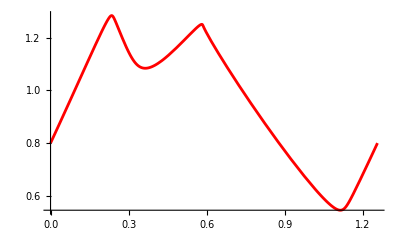
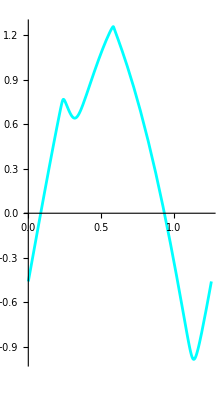

```mathematica
plotex={ParametricPlot[{λ[t],u01[f[t]][[1]]},{t,0,1},PlotStyle->Red],ParametricPlot[{λ[t],u01[f[t]][[2]]},{t,0,1},PlotStyle->Cyan]}
```

```mathematica
t=Import["/Users/michelecastellana/Documents/finite_elements/poisson_equation/solve_u/three_domains/solution/v_1d.csv"];
t= Table[{t[[i,3]],t[[i,1]],t[[i,2]]},{i,2,Length[t]}]
```

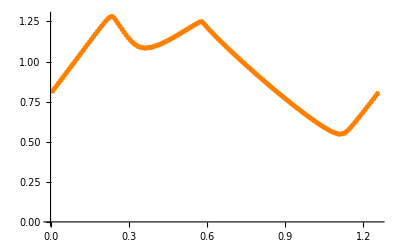
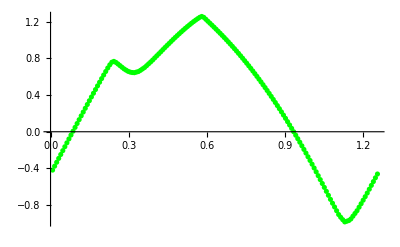

```mathematica
plotnum={ListPlot[Table[{t[[i,1]],t[[i,2]]},{i,1,Length[t]}],PlotStyle->Orange],ListPlot[Table[{t[[i,1]],t[[i,3]]},{i,1,Length[t]}],PlotStyle->Green]}
```

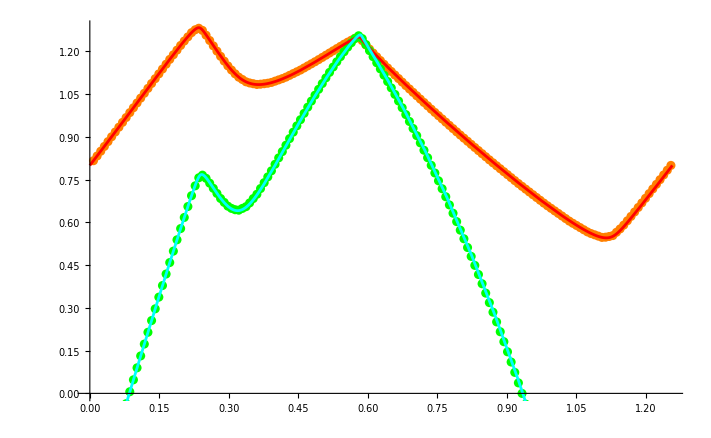

```mathematica
Show[plotnum,plotex]
```

```mathematica
(*2.2 1d -> 2d*)
```

```mathematica
u1[x_]:={Cos[2π x/L],Sin[4π x/L]}
```

```mathematica
plotex={ParametricPlot3D[Flatten[{f[t],u1[λ[t]][[1]]}],{t,0,1},PlotStyle->Red],ParametricPlot3D[Flatten[{f[t],u1[λ[t]][[2]]}],{t,0,1},PlotStyle->Green]}
```

{-Graphics3D-,-Graphics3D-}

```mathematica
t=Import["/Users/michelecastellana/Documents/finite_elements/poisson_equation/solve_u/three_domains/solution/v_2d.csv"];
t= Table[{t[[i,3]],t[[i,4]],t[[i,1]],t[[i,2]]},{i,2,Length[t]}]
```

```mathematica
plotnum={ListPointPlot3D[Table[{t[[i,1]],t[[i,2]],t[[i,3]]},{i,1,Length[t]}],PlotStyle->Orange],ListPointPlot3D[Table[{t[[i,1]],t[[i,2]],t[[i,4]]},{i,1,Length[t]}],PlotStyle->Cyan]}
```

{-Graphics3D-,-Graphics3D-}

```mathematica
Show[plotnum,plotex,PlotRange->Full]
```

-Graphics3D-

```mathematica
(*3 test tensor*)
```

```mathematica
(*3.1 2d -> 1d *)
```

```mathematica
u01[x_]:={
{Cos[2π (x[[1]]x[[2]])],
Sin[2π x[[1]]]-Sin[2π x[[2]]],
(Sin[2π x[[1]]]-Sin[2π x[[2]]])^2},
{Cos[2π x[[1]]]^2-Sin[2π x[[2]]],
Cos[2π x[[1]]]^3-Sin[2π (x[[1]]+x[[2]])],
(Cos[2π x[[1]]]^3-Sin[2π (x[[1]]+x[[2]])])^2}
}
```

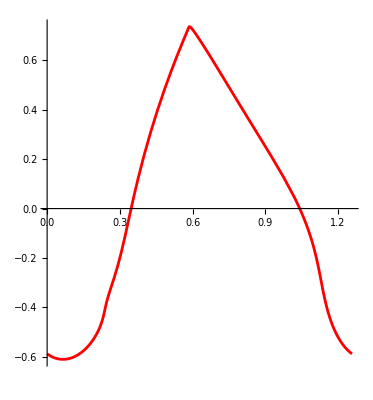
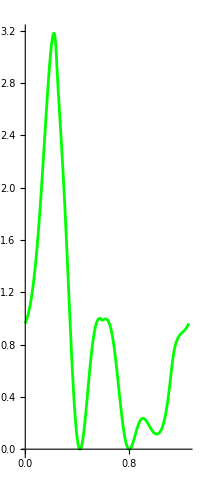

```mathematica
plotex={ParametricPlot[{λ[t],u01[f[t]][[1,1]]},{t,0,1},PlotStyle->Red],ParametricPlot[{λ[t],u01[f[t]][[2,3]]},{t,0,1},PlotStyle->Green]}
```

```mathematica
t=Import["/Users/michelecastellana/Documents/finite_elements/poisson_equation/solve_u/three_domains/solution/t_1d.csv"];
t= Table[{t[[i,7]],t[[i,1]],t[[i,2]],t[[i,3]],t[[i,4]],t[[i,5]],t[[i,6]]},{i,2,Length[t]}]
```

Import::nffil: File /Users/michelecastellana/Documents/finite_elements/poisson_equation/solve_u/three_domains/solution/t_1d.csv not found during Import.

{}

```mathematica
plotnum={ListPlot[Table[{t[[i,1]],t[[i,2]]},{i,1,Length[t]}],PlotStyle->Orange],ListPlot[Table[{t[[i,1]],t[[i,7]]},{i,1,Length[t]}],PlotStyle->Blue]}
```

{-Graphics-,-Graphics-}

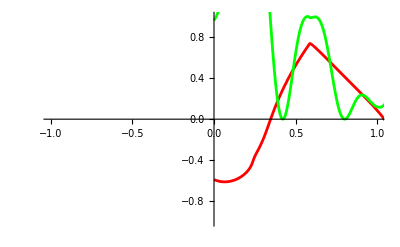

```mathematica
Show[plotnum,plotex]
```